## Functions for modeling

### Linear-solid stiffness matrix

cij0[i], Q0[i] are assumed defined for each layer i

```mathematica
cijCarcione[pars_,ω0_,ω_]:=Module[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},

{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i}=pars;

{(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c33i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c11i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),c13i-(2 c44i ω ((-2+√(1+Q01i^2)+√(1+Q02i^2)) ω+ⅈ (Q01i+Q02i) ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))+c11i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω)+c33i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω),(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c11i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c33i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),(c44i (ω+√(1+Q02i^2) ω+ⅈ Q02i ω0))/((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0),ρi}//N

]
```

```mathematica
cijCarcioneCompiled=
Compile[{{cijQρ,_Real, 1},{ω0,_Real},{ω,_Complex}},
Module[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},

c11i=cijQρ[[1]];
c13i=cijQρ[[2]];
c33i=cijQρ[[3]];
c44i=cijQρ[[4]];
ρi=cijQρ[[5]];
Q01i=cijQρ[[6]];
Q02i=cijQρ[[7]];

{(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c33i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c11i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),c13i-(2 c44i ω ((-2+√(1+Q01i^2)+√(1+Q02i^2)) ω+ⅈ (Q01i+Q02i) ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))+c11i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω)+c33i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω),(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c11i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c33i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),(c44i (ω+√(1+Q02i^2) ω+ⅈ Q02i ω0))/((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0),Re@ρi}

],CompilationTarget->"C", RuntimeOptions->"Speed"
];
```

```mathematica
cijLS[{c11i_,c13i_,c33i_,c44i_,ρi_,Q01i_,Q02i_},ω0_,ω_]:=cijCarcioneCompiled[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},ω0,ω];
```

### Slowness, L1/L2 matrices

Requires run of the cijCarcione function to get frequency-dependent cij[i]

```mathematica
GetLStovasUrsin[{c11i_, c13i_, c33i_, c44i_, ρi_},p_]:=Module[
{L1,L2,d1,d2,d3,d4,d5,qα,qβ,α0,β0,η,δ,σ0,Sα,Sβ,R,R1,R2,req1,req2,imq1,imq2},
α0=√(c33i/ρi);
β0=√(c44i/ρi);
σ0=1-c44i/c33i;
δ=(c13i-c33i+2c44i)/c33i;
η=(c11i c33i-(c13i+2c44i)^2)/(2 c33i^2);
R1=2(1-p^2 β0^2)(δ+2 p^2 α0^2 η)^2;
R2=σ0+2 p^2 β0^2 δ-2 p^2 α0^2(1-2 p^2 β0^2)η;
R=R1/(R2+√(R2^2+2 p^2 β0^2 R1));
Sα=2δ+2 p^2 α0^2 η+R;
Sβ=2(1-p^2 β0^2)α0^2/β0^2 η-R;

d2=√((σ0+δ)/(σ0+Sα));
d3=2 β0^2(σ0+1/2(Sα+δ))/(σ0+δ);
d4=√((σ0-p^2 β0^2(σ0+Sβ))/((1-p^2 β0^2(1+Sβ))(σ0+δ)));
d5=(σ0-2 p^2 β0^2(σ0+1/2(Sβ+δ)))/(σ0+δ);
d1=1/(√(p^2 d3+d5));


req1=Re[1/α0^2-p^2-p^2 Sα];
req2=Re[1/β0^2-p^2-p^2 Sβ];
imq1=Im[1/α0^2-p^2-p^2 Sα];
imq2=Im[1/β0^2-p^2-p^2 Sβ];
imq1=Sign[imq1]imq1;
imq2=Sign[imq2]imq2;
req1=req1;
req2=req2;

qα=√(req1+ⅈ imq1);
qβ=√(req2+ⅈ imq2);

(*qα=1/α0^2-p^2-p^2 Sα;
qβ=1/β0^2-p^2-p^2 Sβ;*)
(*
qα=Sign[Im[qα]]qα;
qβ=Sign[Im[qβ]]qβ;*)



L1=d1{
{d2 √(qα/ρi),1/d4 p/(√(ρi qβ))},
{d3 d2 p √(ρi qα),-d5/d4 √(ρi/qβ)}
};

L2=d1{
{d5/d2 √(ρi/qα),d3 d4 p √(ρi qβ)},
{1/d2 p/(√(ρi qα)),-d4 √(qβ/ρi)}
};

(*{{qα,qβ},{L1,L2}}*)
{{{qα,0},{0,qβ}},L1,L2}
(*l1[j]=L1//N;
l2[j]=L2//N;
q1[j]=qα//N;
q2[j]=qβ//N;*)

]
```

```mathematica
qLCompiled=
Compile[{{cij,_Complex, 1},{ρi,_Real},{p,_Real}},
Module[
{L1,L2,d1,d2,d3,d4,d5,qα,qβ,α0,β0,η,δ,σ0,Sα,Sβ,R,R1,R2},
α0=√(cij[[3]]/ρi);
β0=√(cij[[4]]/ρi);
σ0=1-cij[[4]]/cij[[3]];
δ=(cij[[2]]-cij[[3]]+2cij[[4]])/cij[[3]];
η=(cij[[1]] cij[[3]]-(cij[[2]]+2cij[[4]])^2)/(2 cij[[3]]^2);
R1=2(1-p^2 β0^2)(δ+2 p^2 α0^2 η)^2;
R2=σ0+2 p^2 β0^2 δ-2 p^2 α0^2(1-2 p^2 β0^2)η;
R=R1/(R2+√(R2^2+2 p^2 β0^2 R1));
Sα=2δ+2 p^2 α0^2 η+R;
Sβ=2(1-p^2 β0^2)α0^2/β0^2 η-R;

qα=(Re@#+ⅈ Abs@Im@#)&@√(1/α0^2-p^2-p^2 Sα);
qβ=(Re@#+ⅈ Abs@Im@#)&@√(1/β0^2-p^2-p^2 Sβ);
d2=√((σ0+δ)/(σ0+Sα));
d3=2 β0^2(σ0+1/2(Sα+δ))/(σ0+δ);
d4=√((σ0-p^2 β0^2(σ0+Sβ))/((1-p^2 β0^2(1+Sβ))(σ0+δ)));
d5=(σ0-2 p^2 β0^2(σ0+1/2(Sβ+δ)))/(σ0+δ);
d1=1/(√(p^2 d3+d5));
L1=d1{
{d2 √(qα/ρi),1/d4 p/(√(ρi qβ))},
{d3 d2 p √(ρi qα),-d5/d4 √(ρi/qβ)}
};

L2=d1{
{d5/d2 √(ρi/qα),d3 d4 p √(ρi qβ)},
{1/d2 p/(√(ρi qα)),-d4 √(qβ/ρi)}
};

{{{qα,0},{0,qβ}},L1,L2}
],CompilationTarget->"C", RuntimeOptions->"Speed"
];
```

```mathematica
qL[{c11i_, c13i_, c33i_, c44i_, ρi_},p_?NumericQ]:=qLCompiled[{c11i, c13i, c33i, c44i}, ρi,p];
```

### Reflectivity and transmissivity

```mathematica
(*
REFLECTIVITY ONLY
*)
stackRefExperiment2[ω_?NumericQ,p_?NumericQ,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray, L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[qL[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray](*;
{transArray,refArray, phaseArray}*)
(*foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}]*)
(*;
phaseArray=Exp[ⅈ ω(qABArray d)];
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}]*)
]
```

```mathematica
(*
BOTH REFLECTIVITY AND TRANSMISSIVITY
OUPUT[[1]] IS TRANSMISSIVITY MATRIX
OUPUT[[2]] IS REFLECTIVITY MATRIX
*)
stackRefExperiment2RT[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray, L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,fR,fT},
{qABArray, L1ar, L2ar}=Transpose[qL[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
fR=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
fT=(#1.Inverse[IdentityMatrix[2]+#3.fR[#5,#2,#3,#4]].#2.#4)&;
Fold[
{fT[#1[[1]],#2[[1]],#2[[2]],#2[[3]],#1[[2]]],
fR[#1[[2]],#2[[1]],#2[[2]],#2[[3]]]}&,{{{1,0},{0,1}},{{0,0},{0,0}}},foldArray]
]
```

```mathematica
<<CompiledFunctionTools`
```

```mathematica
stackRefExperiment[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray,L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[GetLStovasUrsin[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray]
]
```

```mathematica
stackRefTransCoefs[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray,L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[GetLStovasUrsin[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
CArray=MapThread[Transpose[#1].#2&,{RotateLeft@L12Array[[;;,2]],L12Array[[;;,1]]}];
DArray=MapThread[Transpose[#1].#2&,{RotateLeft@L12Array[[;;,1]],L12Array[[;;,2]]}];
transArray=2Transpose/@ Inverse/@(CArray+DArray);
refArray=1/2 MapThread[#1.#2&,{Transpose/@(CArray-DArray),transArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray]
]
```

### Time-domain description

```mathematica
addSrcRec[RT_,ω_,zs_,zr_,qAB1_]:=Module[
{exp},

exp[z_]:=Exp[ⅈ ω z qAB1]-{{0,1},{1,0}};

exp[zr].RT.exp[zs]//N//Chop

]

(*
NOTE THAT RPP IS TAKEN FOR INTEGRATION ([[1,1]]) after the StackRefExperiment function
*)

integrand[x_?NumericQ,p_?NumericQ,ω_?NumericQ,CijsAndρ:{{_,_,_,_,_}..},dList_,zs_,zr_]:=With[{p0=p},addSrcRec[stackRefExperiment2[ω,p0,CijsAndρ, dList],ω,zs,zr,qL[CijsAndρ[[1]],p0][[1]]][[1,1]] BesselJ[0,x p0 ω]p0 ω^2]
```

### Numerical testing

```mathematica
binarymodel={
(*shale*)
{22.56,12.38,17.35,3.15,2.38,100,50},
(*sandstone*)
{26.73,12.51,26.73,7.11,2.22,150,100},
(*siltstone*)
{60.13,38.26,50.87,17.17,2.18,100,50}
};
```

```mathematica
nrep=5;
model=ArrayReshape[ConstantArray[binarymodel,{nrep}],{nrep,7}];
```

```mathematica
SeedRandom[2018];
dList=ArrayPad[RandomReal[{0,.1},Length[model]-2],1]/1000;
```

```mathematica
ωcomp=2 Pi 40;
ω0=2Pi 150;
```

```mathematica
cijsNum=cijLS[#,ω0,ωcomp ]&/@model;
```

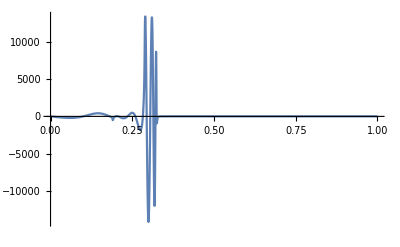

```mathematica
With[{x=0,zs=.1,zr=.2,ω=ωcomp},
Plot[
Re@integrand[x,p,ω,cijsNum,dList,zs,zr],{p,0,1},PlotRange->{Automatic,Full}]
]
```

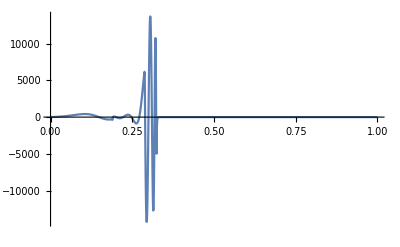

```mathematica
With[{x=0,zs=.1,zr=.2,ω=ωcomp},
Plot[
Im@integrand[x,p,ω,cijsNum,dList,zs,zr],{p,0,1},PlotRange->{Automatic,Full}]
]
```

```mathematica
(*
pars={Method->{"GlobalAdaptive","MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->MachinePrecision,PrecisionGoal->8,AccuracyGoal->Infinity};
*)
Monitor[
zeroX=Table[
With[{x=0,zs=.3,zr=.2,ωc=ω},
NIntegrate[
integrand[x,p,ωc,cijLS[#,ω0,ωc]&/@model,dList,zs,zr],{p,0,.5},Method->{"GlobalAdaptive","MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->MachinePrecision,PrecisionGoal->8,AccuracyGoal->Infinity]
];
,{ω,1,2Pi 150,1}],ω]
```

```mathematica
With[{x=0,zs=.1,zr=.2,ω=ωcomp,p=0.1},
integrand[x,p,ω,cijsNum,dList,zs,zr]
]
```

1.42667+410.51 ⅈ

```mathematica
With[{x=1,zs=.1,zr=.2,ω=ωcomp},
NIntegrate[
integrand[
addSrcRec[
stackRefExperiment2[ω,p0,cijsNum, dList],ω,zs,zr,qL[cijsNum[[1]],p0][[1]]
][[1,1]],x,p0,ω],{p0,0,1}]
]
```

Thread::tdlen: Objects of unequal length in {-11.6605+13.8512 ⅈ,-3.31348-1.70405 ⅈ,-17.943-2.42344 ⅈ,-1.47965-1.63401 ⅈ,-0.992115-0.125333 ⅈ}+{{0,-1},{-1,0}} cannot be combined.

Thread::tdlen: Objects of unequal length in {-55.889-323.025 ⅈ,8.07536+11.2927 ⅈ,316.078+86.9673 ⅈ,-0.480625+4.83554 ⅈ,0.968583+0.24869 ⅈ}+{{0,-1},{-1,0}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{0.,-1.},{-1.,0.}}+{-11.6605+13.8512 ⅈ,-3.31348-1.70405 ⅈ,-17.943-2.42344 ⅈ,-1.47965-1.63401 ⅈ,-0.992115-0.125333 ⅈ} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

NIntegrate::inum: Integrand integrand[{{0,-1.},{-1.,0}},1,p0,80 π] is not numerical at {p0} = {0.00795732}.

NIntegrate[integrand[addSrcRec[stackRefExperiment2[80 π,p0,cijsNum,dList],80 π,0.1,0.2,qL[cijsNum⟦1⟧,p0]⟦1⟧]⟦1,1⟧,1,p0,80 π],{p0,0,1}]

```mathematica
Block[{x=1,zs=.1,zr=.2,ω=ωcomp,p=.2},

integrand[addSrcRec[stackRefExperiment2[ω,p,cijsNum, dList],ω,zs,zr,qL[cijsNum[[1]],p][[1]]][[1,1]],x,p,ω]
]
```

-1.02273+0.0787097 ⅈ

```mathematica
{RepeatedTiming[Table[stackRefExperiment2[ωcomp,p,cijsNum,dList];,{p,0,1,.01}],10][[1]],
RepeatedTiming[Table[stackRefExperiment2RT[ωcomp,p,cijsNum,dList];,{p,0,1,.01}],10][[1]]}
```

{0.693,0.98}

## Stovas and Ursin (2003) and Ursin and Stovas (2002) reflectivity examples

### Single interface reflectivity

Requires precomputed L1/L2 matrices and vertical slowness

```mathematica
RT[LBelow_,LAbove_]:=Module[
{L1a=LAbove[[1]],
L1b=LBelow[[1]],
L2a=LAbove[[2]],
L2b=LBelow[[2]],
C,D,inv,RD,RU,TD,TU},

C=Transpose[L2a].L1b;
D=Transpose[L1a].L2b;
inv=Inverse[C+D];
TD=2inv;
RD=(C-D).inv;
(*TU=TDᵀ;
RU=-RD;*)
{TD,RD}//N
];
```

### Stack reflectivity (recursion)

Requires precomputed L1/L2 matrices and vertical slowness and single interface reflectivities.
Note:
1. each layer has the same index as the bottom interface
2. N layers = N interfaces - 1
3. topmost and bottommost layers are half-spaces with zero thickness

```mathematica
q1[j_Integer,q_]:=q[[j,1]];
q2[j_Integer,q_]:=q[[j,2]];
TD[j_Integer,RT_]:=RT[[j,1]];
RD[j_Integer,RT_]:=RT[[j,2]];
dz[j_Integer,d_]:=d[[j]];
```

```mathematica
e[j_Integer,ω_,q_,d_]:=
{
{Exp[(ⅈ ω q1[j,q] dz[j,d])],0},
{0,Exp[(ⅈ ω q2[j,q] dz[j,d])]}
};

rd[n_Integer,n_Integer,ω_,q_,d_,RT_]:={{0,0},{0,0}};

rd[j_Integer,n_Integer,ω_,q_,d_,RT_]/;j<n:=
rd[j,n,ω,q,d,RT]=e[j,ω,q,d].(RD[j,RT]+Transpose[TD[j,RT]].rd[j+1,n,ω,q,d,RT].Inverse[(IdentityMatrix[2]+RD[j,RT].rd[j+1,n,ω,q,d,RT])].TD[j,RT]).e[j,ω,q,d];
```

```mathematica
ClearAll[phaseFactor];
phaseFactor[ω_,d_/;ArrayQ[d]]:=;
```

```mathematica
ArrayQ[{{1,2,3,45},{1,23,3}}]
```

False

### Rock Physics Input

```mathematica
someFunction[fractureDensity_, waterSaturation_, {ω_,τ0_}]:=Out[{c11, c13, c33, c44, ρbulk}]
```

```mathematica
M[ω]
```

### Declare model

3 interfaces: [number of the interface]
-> chalk/shale (iso)			[1]
-> shale/sandstone (vti) 		[3]
-> siltstone/sandstone (vti)	[5]

Model parameters : {c11, c13, c33, c44, ρ, Q1, Q2}

```mathematica
model={
(*chalk (iso)*)
{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den,350,350}/.vp->4.5/.vs->2.5/.den->2.75,
(*shale (iso)*)
{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den,100,50}/.vp->2.92/.vs->1.4/.den->2.18,
(*shale*)
{22.56,12.38,17.35,3.15,2.38,100,50},
(*sandstone*)
{26.73,12.51,26.73,7.11,2.22,150,100},
(*siltstone*)
{60.13,38.26,50.87,17.17,2.18,100,50},
(*sandstone*)
{26.73,12.51,26.73,7.11,2.22,150,100}
};
```

Layer thickness is computed randomly for further tests

```mathematica
dList=
Join[{0},SeedRandom[2018];RandomReal[{0,.1},Length[model]-2],{0}];
```

```mathematica
model[[1]]//Length
```

7

```mathematica
RTinterface2[.1]//Length
```

6

Get frequency-dependent cij, matrices L1/L2 and slowness for a given f0 and a given signal frequency f

```mathematica
f0=150;
f=40;
ωcomp=2Pi f;

qList=ConstantArray[0,{Length[model],2}];
LList=ConstantArray[0,{Length[model],2,2,2}];

Table[
{qList[[i]],LList[[i]]}=GetLStovasUrsin[
cijCarcione[model[[i]],f0,ωcomp]
,p];
,{i,1,Length[model]}
];
```

```mathematica
qp[p_, f_:f0,ω_:ωcomp]:=GetLStovasUrsin[cijCarcione[#,f,ω],p]&/@model;
```

```mathematica
RTinterface2[p_, f_:f0, ω_:ωcomp]:=Module[{q,L},
{q,L}=Transpose@qp[p,f, ω];
MapThread[RT,{RotateLeft@L,L}]
];
```

```mathematica
SetAttributes[RTinterface2, Listable]
```

```mathematica
ClearAll@RTinterface2
```

```mathematica
Plot3D[Re@RTinterface2[s,f0,ω][[1,1,1,1]],{s,0,.1},{ω,2π 10,2π 200}]
```

Calculate reflection-transmission coefficients for each interface

```mathematica
Clear[RTinterface];
```

```mathematica
RTinterface[i_]:=
RT[LList[[i+1]],LList[[i]]];
```

```mathematica
pvec=Table[p,{p,0,.3,.0025}];
rtest=Table[RTinterface[i,#],{i,1,Length@model-1}][[2,2]]&/@pvec;
```

```mathematica
Table[RTinterface[i,#],{i,1,Length@model-1}][[2,2]]&/@pvec[[1;;2]]
```

{{{((1) (-((18-1) 5 1)/(√(1+1) √1)+4))/(-1. (-1/(√(1+1) 1)+1+1-1/1) (5+1/1)11)+1/1,1},{1}},1}
 |  |  |  |

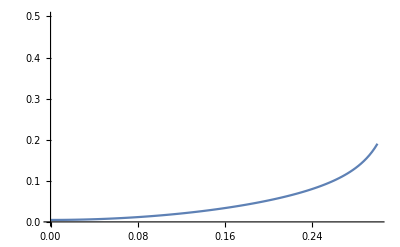

```mathematica
ListPlot[{pvec,-Re@rtest[[All,1,1]]}ᵀ,Joined->True,PlotRange->{{0,0.3},{0,.5}}]
```

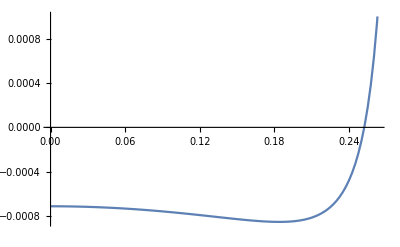

```mathematica
ListPlot[{pvec,Im@rtest[[All,1,1]]}ᵀ,Joined->True,PlotRange->{{0,0.3},{0.001,-.008}}]
```

Calculate the response of the stack at a fixed p

```mathematica
Block[{p=.1},rd[1,Length[model],ωcomp,qList,dList,RTinterface2[p]]//N]
```

{{0.356687-0.0942922 ⅈ,0.145405-0.125876 ⅈ},{0.145405-0.125876 ⅈ,-0.292743+0.0493532 ⅈ}}

## Stovas and Ursin (2003) Well - log example

### Load and prepare the data

Null

```mathematica
Null
```

```mathematica
Null
```

Null

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

### Calculate the RT response

#### for a fixed frequency/slowness pair

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### for a range of frequency / wavenumbers

predefine arrays

```mathematica
fList=Table[i,{i,1,101,.5}];
pList=Table[i,{i,0,.25,.00125}];
kList=Table[2Pi fList[[fj]]pList[[pj]],{fj,1,Length[fList]},{pj,1,Length[pList]}];

output=ConstantArray[0,{Length[fList],Length[pList],2,2}];
```

loop over frequency/wavenumber

```mathematica
If[Length[fList]≥Length[pList],
listLong=fList;listShort=pList;
writeOut[jS_,jL_,writeFrom_]:=output[[jL,jS]]=writeFrom;
pf[jS_,jL_]:={pList[[jS]],fList[[jL]]}
,
listLong=pList;listShort=fList;
writeOut[jS_,jL_,writeFrom_]:=output[[jS,jL]]=writeFrom;
pf[jS_,jL_]:={pList[[jL]],fList[[jS]]};
];
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null